```mathematica
SetDirectory["C:\\Users\\Caden Gobat\\Documents\\GitHub\\PHYS-3181\\homework2"]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework2

```mathematica
coarseDataNaive=ReadList["p1_025_naive.log",{Number,Number}]
coarseDataMP=ReadList["p1_025_midpoint.log",{Number,Number}]
medDataNaive=ReadList["p1_010_naive.log",{Number,Number}]
medDataMP=ReadList["p1_010_midpoint.log",{Number,Number}]
fineDataNaive =ReadList["p1_002_naive.log",{Number,Number}]
fineDataMP=ReadList["p1_002_midpoint.log",{Number,Number}]
```

{{0.,0.},{0.25,0.275242},{0.5,0.609021},{0.75,1.01555},{1.,1.51244}}

{{0.,0.},{0.25,0.283287},{0.5,0.647035},{0.75,1.1141},{1.,1.71382}}

{{0.,0.},{0.1,0.115698},{0.2,0.243624},{0.3,0.344637},{0.4,0.541727},{0.5,0.715074},{0.6,0.797702},{0.7,1.11965},{0.8,1.35522},{0.9,1.61627},{1.,1.6338}}

{{0.,0.},{0.1,0.116278},{0.2,0.246073},{0.3,0.349846},{0.4,0.55267},{0.5,0.733177},{0.6,0.821995},{0.7,1.15953},{0.8,1.41052},{0.9,1.69066},{1.,1.71757}}

{{0.,0.},{0.02,0.020197},{0.04,0.040794},{0.06,0.063074},{0.08,0.08322},{0.1,0.105066},{0.12,0.13005},{0.14,0.153284},{0.16,0.173233},{0.18,0.201173},{0.2,0.22096},{0.22,0.251018},{0.24,0.270599},{0.26,0.296159},{0.28,0.329635},{0.3,0.34881},{0.32,0.375922},{0.34,0.403572},{0.36,0.442091},{0.38,0.471643},{0.4,0.48986},{0.42,0.519772},{0.44,0.550279},{0.46,0.595965},{0.48,0.628636},{0.5,0.645483},{0.52,0.678487},{0.54,0.73068},{0.56,0.766084},{0.58,0.781488},{0.6,0.817196},{0.62,0.876664},{0.64,0.915031},{0.66,0.954176},{0.68,0.96727},{0.7,1.00667},{0.72,1.07644},{0.74,1.08785},{0.76,1.16215},{0.78,1.17228},{0.8,1.21576},{0.82,1.29735},{0.84,1.30534},{0.86,1.39212},{0.88,1.39852},{0.9,1.44651},{0.92,1.54162},{0.94,1.54536},{0.96,1.64642},{0.98,1.6482},{1.,1.70116}}

{{0.,0.},{0.02,0.020201},{0.04,0.040811},{0.06,0.063112},{0.08,0.083287},{0.1,0.105171},{0.12,0.130206},{0.14,0.153499},{0.16,0.173511},{0.18,0.201535},{0.2,0.221403},{0.22,0.251571},{0.24,0.271249},{0.26,0.29693},{0.28,0.33056},{0.3,0.349858},{0.32,0.377127},{0.34,0.404947},{0.36,0.443686},{0.38,0.473439},{0.4,0.491823},{0.42,0.52196},{0.44,0.552705},{0.46,0.598713},{0.48,0.631661},{0.5,0.648719},{0.52,0.682025},{0.54,0.734637},{0.56,0.770386},{0.58,0.786034},{0.6,0.822114},{0.62,0.882117},{0.64,0.920906},{0.66,0.960494},{0.68,0.97387},{0.7,1.01374},{0.72,1.08422},{0.74,1.09593},{0.76,1.17102},{0.78,1.18146},{0.8,1.22553},{0.82,1.30803},{0.84,1.31635},{0.86,1.40414},{0.88,1.41088},{0.9,1.45958},{0.92,1.55587},{0.94,1.55996},{0.96,1.6623},{0.98,1.66443},{1.,1.71825}}

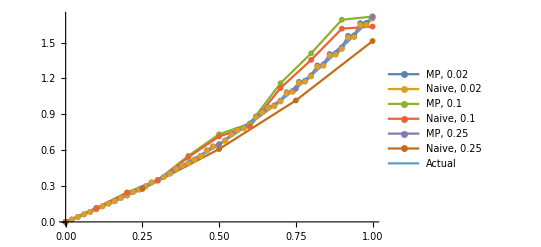

```mathematica
ListLinePlot[{fineDataMP,fineDataNaive,medDataMP,medDataNaive,coarseDataMP,coarseDataNaive,Table[{x,Exp[x]-1},{x,0,1,0.01}]},PlotLegends->{"MP, 0.02","Naive, 0.02","MP, 0.1","Naive, 0.1","MP, 0.25","Naive, 0.25","Actual"},PlotMarkers->Append[Table[{"●",6},6],{None,4}]]
```

```mathematica
Append[Table["●",6],None]
```

{●,●,●,●,●,●,None}